# Neural Network In Wolfram Language

## The LeNet Model

```mathematica
leNet=NetModel["LeNet Trained on MNIST Data"]
```

NetChain[<11>]

-Graphics-

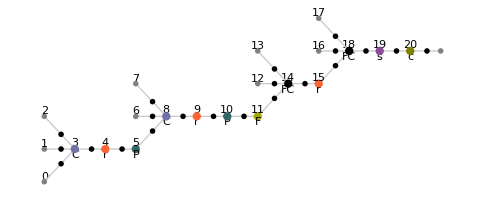

```mathematica
Information[leNet,"FullSummaryGraphic"]
Information[leNet,"MXNetNodeGraphPlot"]
```

## Performance on the MNIST Test Dataset1

The LeNet Model is known to have achieved 98.5% accuracy on the MNIST dataset.

https://resources.wolframcloud.com/NeuralNetRepository/resources/LeNet-Trained-on-MNIST-Data/

## Extracting and Inspecting Layers

#### Convolution Layer

```mathematica
NetExtract[net,1]
```

ConvolutionLayer[…]

```mathematica
NetExtract[net,{1,"Weights"}]//Normal
```

## Bibliography

1	Y. LeCun, L. Bottou, Y. Bengio, P. Haffner, "Gradient-Based Learning Applied to Document Recognition," Proceedings of the IEEE, 86(11), 2278-2324 (1998)
Available from: http://yann.lecun.com/exdb/lenet